Let us try to do square lattice

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
Clear[Energy];Energy[k_] := Energy[k] = -2(Cos[k[[1]]]+Cos[k[[2]]]);
```

```mathematica
Clear[HamMFU];HamMFU[nup_, ndn_, spls_, smns_]:= HamMFU[nup,ndn, spls, smns] = {{ ndn, -smns},{-spls, nup}};
```

```mathematica
Clear[HamMFull];HamMFull[nup_, ndn_, spls_, smns_,k_,μ_,U_]:= HamMFull[nup,ndn, spls, smns,k,μ,U]= Energy[k] IdentityMatrix[2] +U HamMFU[nup,ndn, spls, smns] - μ IdentityMatrix[2];
```

```mathematica
Clear[EnerMF];EnerMF[nup_, ndn_, spls_, smns_,k_,μ_,U_] := EnerMF[nup,ndn, spls, smns,k,μ,U]= Chop[  N[Sort[Eigenvalues[HamMFull[nup,ndn, spls, smns,k,μ,U] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[nup_, ndn_, spls_, smns_,k_,μ_,U_] :=ULiebMF[nup,ndn, spls, smns,k,μ,U]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[HamMFull[nup,ndn, spls, smns,k,μ,U]  ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Clear[IJMat];IJMat[i_,j_,N_]:= ArrayFlatten[ Table[ If[i1==i&&j1==j,1,0],{i1,1,N},{j1,1,N}]];
```

```mathematica
Clear[nupMF];nupMF[nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=nupMF[nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[nup,ndn, spls, smns,k,μ,U][[band]]]Module[{um = ULiebMF[nup,ndn, spls, smns,k,μ,U]}, (um†.(IJMat[1,1,2]).um)[[band,band]]],{band,1 ,2},{k,kSpan[krange]}];
```

```mathematica
Clear[ndnMF];ndnMF[nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=ndnMF[nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[nup,ndn, spls, smns,k,μ,U][[band]] ]Module[{um = ULiebMF[nup,ndn, spls, smns,k,μ,U],zr = {0,0,0}}, (um†.(IJMat[2,2,2]).um)[[band,band]]],{band,1 ,2},{k,kSpan[krange]}];
```

```mathematica
Clear[splsMF];splsMF[nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=splsMF[nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[nup,ndn, spls, smns,k,μ,U][[band]] ]Module[{um = ULiebMF[nup,ndn, spls, smns,k,μ,U],zr = {0,0,0}}, (um†.(-IJMat[2,1,2]).um)[[band,band]]],{band,1 ,2},{k,kSpan[krange]}];
```

```mathematica
Clear[smnsMF];smnsMF[nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=smnsMF[nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[nup,ndn, spls, smns,k,μ,U][[band]] ]Module[{um = ULiebMF[nup,ndn, spls, smns,k,μ,U]}, (um†.(-IJMat[1,2,2]).um)[[band,band]]],{band,1 ,2},{k,kSpan[krange]}];
```

```mathematica
Clear[NumEq];NumEq[nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=NumEq[nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[nup,ndn, spls, smns,k,μ,U][[band]] ],{band,1 ,2},{k,kSpan[krange]}];
```

```mathematica
Clear[FindMu];FindMu[nup_, ndn_, spls_, smns_,U_,fil_,β_,krange_] :=FindMu[nup,ndn, spls, smns,U,fil,β,krange]=μ/.FindRoot[ NumEq[nup,ndn, spls, smns,U,μ,β,krange]-fil,{μ,-10,10},Evaluated->False, MaxIterations->20,PrecisionGoal->3];
```

```mathematica
Clear[ItrFnMF];ItrFnMF[U_,fil_,β_,krange_]:= ItrFnMF[U,fil,β,krange]=  NestList[ {FindMu[#[[2]],#[[3]], #[[4]],#[[5]],U,fil,β,krange],nupMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],ndnMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange] , splsMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],smnsMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange]}&,{U,RandomReal[],RandomReal[],RandomReal[],RandomReal[]},10][[10]];
```

```mathematica
Clear[ItrFnMFCheck];ItrFnMFCheck[U_,fil_,β_,krange_]:= ItrFnMFCheck[U,fil,β,krange]=  NestList[ {FindMu[#[[2]],#[[3]], #[[4]],#[[5]],U,fil,β,krange],nupMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],ndnMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange] , splsMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],smnsMF[#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange]}&,{U,RandomReal[],RandomReal[],RandomReal[],RandomReal[]},10];
```

```mathematica
Block[{U=0.0,fil=0.7, β=100, krange=30},Module[{itr=ItrFnMFCheck[U,fil,β,krange]}, itr]]
```

General::munfl: 2.542667498139×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.401912821049×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.056240437322×10^-357 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.,0.416681,0.144219,0.378146,0.36382},{-0.7311,0.5,0.5,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.},{-0.7311,0.35,0.35,0.,0.}}

```mathematica
NumEq[0,0,0,0,0.0,-0.7310997039471169,100,30]
```

0.7

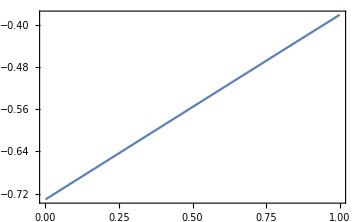

```mathematica
Block[{fil=0.7, β=100, krange=30},DiscretePlot[ItrFnMF[U,fil,β,krange][[1]], {U,0,1,0.1}]]
```

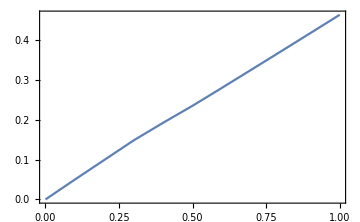

```mathematica
Block[{fil=1.0, β=100, krange=30},DiscretePlot[ItrFnMF[U,fil,β,krange][[1]], {U,0,1,0.1}]]
```